#### Лабораторная работа 5 Численное дифференцирование и интегрирование Вариант 8

Задание 1. Найти приближенные значения производных первого и второго порядков функции f (x) в точке x_0, используя:
а) функцию D системы Mathematica;
б)  формулы численного дифференцирования y'_i≈1/h(Δy_i-1/2 Δ^2 y_i+1/3 Δ^3 y_i) и y''_i≈1/h^2(Δ^2 y_i-Δ^3 y_i) для шага h_1 = 0,1 и шага h_2 = 0,01. Сравнить полученные значения.

	1.8. f(x) = cos^3(x^2+√x), x_0=5,37.

```mathematica
f[x_]=(Cos[x^2+√x])^3; x0 = 5.37; h1=0.1; h2=0.01;
```

а) Найдём приближенное значение производной первого порядка, используя функцию D.

```mathematica
d1=D[f[x],x]/.x->x0
```

7.93433

Найдём приближенное значение производной второго порядка, используя функцию D.

```mathematica
d2=D[f[x],{x,2}]/.x->x0
```

-276.544

б) Введём формулы для вычисления конечных разностей:

```mathematica
dif1[x_,h_]=f[x+h]-f[x];
dif2[x_, h_]=dif1[x+h,h]-dif1[x,h];
dif3[x_, h_]=dif2[x+h,h]-dif2[x,h];
```

Введем функции для приближенного вычисления производных:

```mathematica
pro1[x_,h_] = 1/h(dif1[x,h]-1/2 dif2[x,h]+1/3 dif3[x,h]);
pro2[x_,h_]=1/h^2(dif2[x,h]-dif3[x,h]);
```

Результат численного дифференцирования для шага h_1=0.1:

```mathematica
pro1[x0,h1]
pro2[x0,h1]
```

-7.25496

25.0539

Результат численного дифференцирования для шага h_2=0.01:

```mathematica
pro1[x0,h2]
pro2[x0,h2]
```

-7.25496

25.0539

При сравнении можно заметить, что результат численного дифференцирования для шага h_2 намного ближе к реальным значениям производной в этой точке, чем для шага h_1. Для первой производной погрешность намного меньше, чем для второй.

Задание 2. 
а) Вычислить с помощью формулы второго порядка точности и составить таблицу приближенных значений y'_i производной функции f(x) на отрезке [-1, 3] с шагом h = 0,2;
б)  Изобразить на одном чертеже (на отрезке [-1, 3]) график функции f' (x), полученной с помощью функции D пакета Mathematica, и точки (x_i,y'_i) , соответствующие приближенным значениям производной, найденные в пункте а.

		2.8. f(x) = (√(1+x^3))/(sin^2(7x+1)).

```mathematica
f[x_]=(√(1+x^3))/(Sin[7x+1])^2; a=-1; b =3; h = 0.2;
```

a) Приближенная формула для первой производной  второго порядка точности:

```mathematica
pro [x_] = (f[x+h]-f[x-h])/(2h);
```

Составим таблицу приближенных значений производной:

```mathematica
TableForm[Table[{a+h*i,pro[a+h*i]},{i,0,(b-a)/h}]]
```

-1. | 1.76867-2.641 ⅈ
-0.8 | 649.616
-0.6 | 0.781656
-0.4 | -633.197
-0.2 | 0.98038
0. | -10.9183
0.2 | 3.35756
0.4 | -1.96918
0.6 | 24.7844
0.8 | 0.079858
1. | 6695.3
1.2 | 1.4152
1.4 | -6683.
1.6 | 3.82526
1.8 | -26.2419
2. | 12.1021
2.2 | -4.93659
2.4 | 70.4632
2.6 | -0.427103
2.8 | 168760.
3. | 2.54325

б) Изобразим график производной, полученной с помощью функции D пакета Mathematica, и точки (x_i,y'_i) найденные в пункте а.

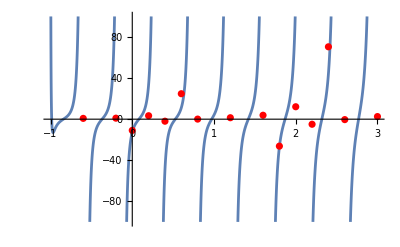

```mathematica
dif[x_]=D[f[x],x];
graphic1 = Plot[dif[x],{x,a,b},PlotRange->{{-1,3}, {-100, 100}}];
graphic2 = ListPlot[Table[{a+h*i,pro[a+h*i]},{i,0,(b-a)/h}], PlotStyle->Red];
Show[graphic1, graphic2]
```

Задание 3. Вычислить определенный интеграл: 
а) по формуле средних прямоугольников; 
б) по формуле трапеций. 
В обоих случаях использовать двойной просчет при n_1= 8 и n_2= 10 для уточнения 
значения интеграла по Ричардсону.

		3.8. ∫_0.8^1.6 (√(2x+2.8))/(0.7 x^2+√(x^2+1.3))ⅆx

```mathematica
f[x_] =(√(2x+2.8))/(0.7 x^2+√(x^2+1.3));a=0.8; b=1.6;
```

а) Формула средних прямоугольников:

Для n = 8:

```mathematica
n1=8;
```

```mathematica
Int1 = (b-a)/n1*∑_(i=1)^n1 f[(a+(i-1)*(b-a)/n1)+ (b-a)/(2n1)]
```

0.695637

Для n = 10:

```mathematica
n2 = 10;
```

```mathematica
Int2 = (b-a)/n2*∑_(i=1)^n2 f[(a+(i-1)*(b-a)/n2)+ (b-a)/(2n2)]
```

0.695693

Уточнение значений интеграла по Ричардсону (для средних прямоугольников: k = 2)

```mathematica
k =2;
Int = Int2+n1^k/(n2^k-n1^k)*(Int2-Int1)
```

0.695791

б) Формула трапеций:

Для n = 8:

```mathematica
Int1=(b-a)/n1(f[a]/2+Sum[f[a+(b-a)/n1*i],{i,1,n1-1}]+f[b]/2)
```

0.696099

Для n = 10:

```mathematica
Int2=(b-a)/n2(f[a]/2+Sum[f[a+(b-a)/n2*i],{i,1,n2-1}]+f[b]/2)
```

0.695988

Уточнение значений интеграла по Ричардсону (для трапеций:  k = 2)

```mathematica
Int = Int2+n1^k/(n2^k-n1^k)*(Int2-Int1)
```

0.695791

Задание 4. Вычислить определенный интеграл от таблично заданной функции по формуле Симпсона (парабол) для разбиений отрезка интегрирования на 8 и на 16 частей.

```mathematica
X16 = {{1.04,0.9519},{1.1,0.9181},{1.16,0.8534},{1.22,0.8278},{1.28,0.7734},{1.34,0.7537},{1.4,0.7071},{1.46,0.6917},{1.52,0.6513},{1.58,0.6392},{1.64,0.6036},{1.7,0.5941},{1.76,0.5625},{1.82,0.5549},{1.88,0.5265},{1.94,0.5206},{2.,0.4950}};
```

```mathematica
X8 = Table[X16[[i]],{i,1,17,2}]
```

{{1.04,0.9519},{1.16,0.8534},{1.28,0.7734},{1.4,0.7071},{1.52,0.6513},{1.64,0.6036},{1.76,0.5625},{1.88,0.5265},{2.,0.495}}

Для n = 8:

```mathematica
Answer1 =(X8[[9,1]]-X8[[1,1]])/(3*2n1)*(X8[[1, 2]] + X8[[9, 2]] + 4 * Sum[X8[[i+1, 2]],{i, 1, n1 - 1,2}] + 2 * Sum[X8[[i+1, 2]],{i,  2, n1 - 2, 2}])
```

0.323674

Для n = 16:

```mathematica
Answer2 =(X16[[17,1]]-X16[[1,1]])/(3*2n2)*(X16[[1, 2]] + X16[[17, 2]] + 4 * Sum[X16[[i+1, 2]],{i, 1, n2 - 1,2}] + 2 * Sum[X16[[i+1, 2]],{i,  2, n2 - 2, 2}])
```

0.363829

Задание 5. Вычислить определенный интеграл с помощью квадратурной формулы Гаусса с n узлами.
		
			5.8. ∫_1.6^3.2 (3+cos(x+2))/(x+2.4)ⅆx, n = 6.

```mathematica
f[x_]=(3+Cos[x+2])/(x+2.4); a=1.6; b = 3.2;n=6;
```

Список корней сохраним под именем listt:

```mathematica
sl = NSolve[LegendreP[n,t]==0,t];
```

```mathematica
listt=t/.sl
```

{-0.93247,-0.661209,-0.238619,0.238619,0.661209,0.93247}

Для определения квадратурных коэффициентов Гаусса Ai решим линейную систему. Введем матрицу ее коэффициентов T и столбец свободных членов B:

```mathematica
MatrixForm[T=Table[If[i==1,1,(listt[[j]])^(i-1)],{i,n},{j,n}]]
```

(1 | 1 | 1 | 1 | 1 | 1
-0.93247 | -0.661209 | -0.238619 | 0.238619 | 0.661209 | 0.93247
0.869499 | 0.437198 | 0.0569391 | 0.0569391 | 0.437198 | 0.869499
-0.810782 | -0.289079 | -0.0135868 | 0.0135868 | 0.289079 | 0.810782
0.756029 | 0.191142 | 0.00324206 | 0.00324206 | 0.191142 | 0.756029
-0.704974 | -0.126385 | -0.000773618 | 0.000773618 | 0.126385 | 0.704974)

```mathematica
B=Table[If[EvenQ[i]==True, 0, 2/i], {i, n}]//N
```

{2.,0.,0.666667,0.,0.4,0.}

Найдём квадратурные коэффициенты:

```mathematica
A=LinearSolve[T,B]
```

{0.171324,0.360762,0.467914,0.467914,0.360762,0.171324}

Вычислим определенный интеграл с помощью квадратурной формулы Гаусса с 6 узлами:

```mathematica
int= (b-a)/2∑_(i=1)^n (A[[i]]*f[(b+a)/2+(b-a)/2*tt[[i]]])
```

0.903332